# テキストブロック推測

## 定数設定

テキスト抽出プログラムと同じ定数を使う。

```mathematica
repod="/Users/kouamano/gitsrc/utility/text_op/"
```

/Users/kouamano/gitsrc/utility/text_op/

上記ディレクトリでgit pull しておく。

```mathematica
repof="mupdftotxblock.py"
```

mupdftotxblock.py

```mathematica
repoImpt=Import[repod<>repof,"Text"];
```

```mathematica
ss=StringPosition[repoImpt,"# config start"][[1,2]]
se=StringPosition[repoImpt,"# config end"][[1,1]]
```

38

134

```mathematica
rlStr=StringSplit[StringTake[repoImpt,{ss+2,se-2}],"\n"]
```

{pgRECTS = '!![[',pgRECTE = ']]',blDLM = '>>>',bbS = '[[[',bbE = ']]]',txS = '{{{',txE = '}}}'}

```mathematica
exStr=StringReplace[rlStr,"'"->"\""]
```

{pgRECTS = "!![[",pgRECTE = "]]",blDLM = ">>>",bbS = "[[[",bbE = "]]]",txS = "{{{",txE = "}}}"}

変数の確認

```mathematica
valStr=Map[StringSplit[#," = "][[1]]&,exStr]
```

{pgRECTS,pgRECTE,blDLM,bbS,bbE,txS,txE}

変数アサイン実行

```mathematica
exStr//ToExpression
```

{!![[,]],>>>,[[[,]]],{{{,}}}}

その他の変数

```mathematica
pgRectSstr="Rect("
pgRectEstr=") "
```

Rect(

)

## File

```mathematica
dir="/Users/kouamano/Downloads/testdata/"
```

/Users/kouamano/Downloads/testdata/

```mathematica
file="019f877a-9000-75ac-a3ca-42d2a8186f25.mpt"
```

019f877a-9000-75ac-a3ca-42d2a8186f25.mpt

```mathematica
file2="hca.mpt"
```

hca.mpt

## Refine

refine対象

```mathematica
impt=Import[dir<>file,"TEXT"];
```

以下、refine処理

```mathematica
refinePgRect[str_]:=Module[{posS,posE,coordstr,coord},
posS=StringPosition[str,pgRectSstr][[1,2]]+1;
posE=StringPosition[str,pgRectEstr][[1,1]]-1;
(*coordstr="{"<>StringTake[str,{posS,posE}]<>"}"*);
coord=ToExpression["{"<>StringTake[str,{posS,posE}]<>"}"];
coord
]
```

```mathematica
refinebbRect[str_]:=Module[{posS,posE,coordstr,coord},
posS=StringPosition[str,bbS][[1,2]]+3;
posE=StringPosition[str,bbE][[1,1]]-3;
(*coordstr="{"<>StringTake[str,{posS,posE}]<>"}"*);
coord=ToExpression["{"<>StringTake[str,{posS,posE}]<>"}"];
coord
]
```

```mathematica
refinebbText[str_]:=StringReplace[str,RegularExpression["\}\}\}\n*"]->"\n"]
```

```mathematica
refinebb[bblist_]:={refinebbRect[bblist[[1]]],refinebbText[bblist[[2;;]]]}
```

```mathematica
refinePg[pglist_]:={pglist[[1]],Map[refinebb,pglist[[2]]]}
```

第0段階のrefine

```mathematica
imptPg=Map[StringSplit[#,blDLM]&,StringSplit[impt,pgRECTS]];
```

第1段階のrefine

```mathematica
refine1=DeleteCases[Map[{refinePgRect[#[[1]]],Map[StringSplit[#,txS]&,#[[2;;]]]}&,imptPg],{"\n"},Infinity];
```

第2段階のrefine

```mathematica
refine2=Map[refinePg,refine1];
```

Total refine

```mathematica
docrefine[doc_]:=Module[{imptPg,refine1},
imptPg=Map[StringSplit[#,blDLM]&,StringSplit[doc,pgRECTS]];
refine1=DeleteCases[Map[{refinePgRect[#[[1]]],Map[StringSplit[#,txS]&,#[[2;;]]]}&,imptPg],{"\n"},Infinity];
Map[refinePg,refine1]
]
```

```mathematica
refine3=docrefine[impt];
```

```mathematica
refine2==refine3
```

True

## ブロック判定

概要

座標：{x0,y0,x1,y1}、原点は左上(0,0)

垂直ブロック成分（範囲）

垂直ブロックごとの水平ブロック成分（範囲）

垂直ブロックの並びを作る

水平ブロックの並びを作る

変数

マージン(20~25mm)(縦：6~10% / 横：7~10% / A4)

ノンブル/柱範囲

本文範囲

行高さ(2.45~4.2mm)(0.8~1.4%)

参照値設定

- マージン縦(比)

```mathematica
mgVMax=0.1
mgVMin=0.06
mgHMax=0.1
mgHMin=0.07
```

0.1

0.06

0.1

0.07

- 行高さ(比)

```mathematica
lineHeightMax=0.014
lineHeigthMin=0.008
```

0.014

0.008

注意点

- ブロックでソートすると、却ってテキストの並び順が不適切となる。（pymupdfでは左右カラム順がかなり正しく抽出されている）

### 垂直ブロック抽出(1)

ページサイズ：

```mathematica
pgSize=Map[#[[1]]&,refine3]
```

{{0.,0.,595.276,841.89},{0.,0.,595.276,841.89},{0.,0.,595.276,841.89},{0.,0.,595.276,841.89},{0.,0.,595.276,841.89}}

```mathematica
pgXMax=Map[#[[3]]&,pgSize]//Max
pgYMax=Map[#[[4]]&,pgSize]//Max
```

595.276

841.89

テキストブロック（ページごと）：

```mathematica
pgText=Map[Cases[#,{{_,_,_,_},{__}},{2}]&,refine3];
```

```mathematica
(pgTxCoord=Map[#[[1]]&,pgText,{2}])//Length
```

5

```mathematica
(Yspans=Map[{#[[2]],#[[4]]}&,pgTxCoord,{2}])//Length
```

5

```mathematica
(Yitvl=MapApply[Interval,Yspans])//Length
```

5

```mathematica
WYitvl=Apply[Interval,Cases[Yitvl,List[_,_],Infinity]]
```

Interval[{61.4803,88.1883},{107.48,148.196},{149.41,176.204},{177.488,218.216},{219.5,288.236},{289.492,330.236},{331.41,358.244},{359.488,512.288},{513.41,540.296},{541.411,568.484},{569.318,582.308},{583.322,596.312},{597.411,610.316},{611.41,624.32},{625.334,638.324},{639.358,652.328},{653.411,694.484},{695.318,708.344},{709.48,722.348},{723.382,736.352},{737.484,750.356},{751.462,764.36}]

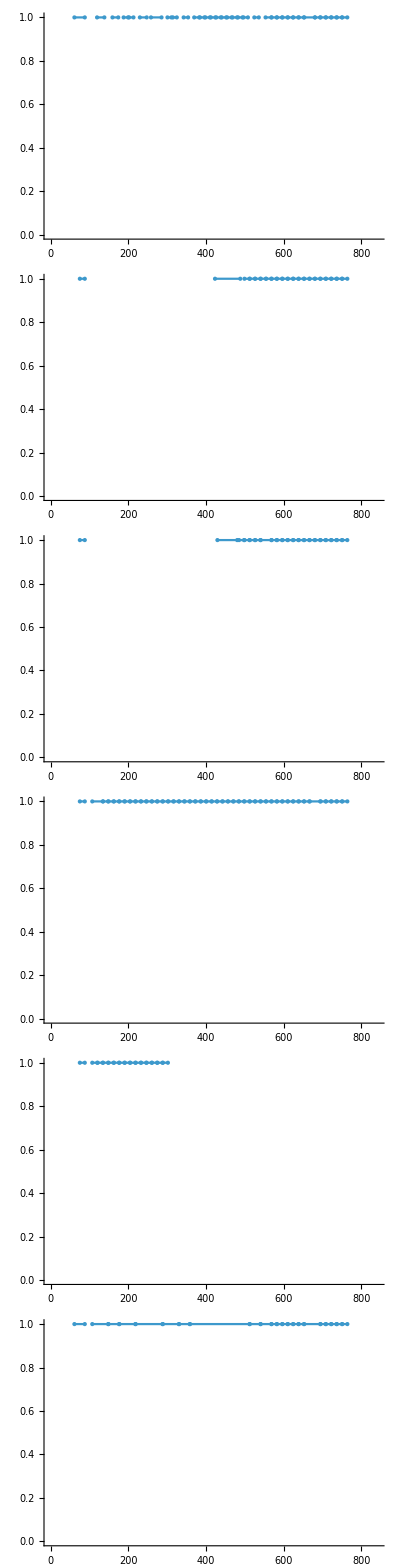

```mathematica
Map[NumberLinePlot[#,PlotRange->{0,841.89},ImageSize->800]&,Append[Yitvl,WYitvl]]//TableForm
```

```mathematica
refine3[[1]][[2]];
```

### 水平ブロック抽出(1)

水平ブロック抽出では被覆領域のカウントを利用する。

```mathematica
Get["/Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/NumberTheory.txt"]
```

```mathematica
(Xspans=Map[{#[[1]],#[[3]]}&,pgTxCoord,{2}])//Length
```

5

```mathematica
(Xitvl=Map[coverageDensity[{0,pgXMax},#]&,Xspans])//Length
```

5

```mathematica
(WXitvl=coverageDensity[{0,pgXMax},Cases[Xspans,{_,_},{2}]])//Length
```

178

```mathematica
(WXitvlP=Cases[WXitvl,{_,_,z_}/;z>0])//Length
```

176

```mathematica
Map[#[[3]]&,WXitvlP]//Sort
```

{2,3,3,4,4,5,6,7,8,9,10,10,11,11,12,13,14,15,16,16,17,18,18,19,20,21,22,23,24,25,25,26,26,27,27,28,28,28,28,29,30,31,31,32,33,33,34,35,35,36,36,37,38,39,40,41,42,42,43,44,44,44,45,46,47,48,48,49,49,50,51,53,57,59,62,63,63,74,76,78,78,80,81,82,83,84,84,85,85,86,87,88,88,88,89,90,90,91,91,91,92,93,94,94,95,96,97,97,97,98,98,100,100,100,101,101,102,102,103,103,104,104,105,105,106,107,107,108,108,108,109,109,109,110,110,110,110,111,111,111,111,112,112,112,112,112,113,113,113,114,114,115,115,115,116,116,116,117,117,118,118,118,119,119,120,120,120,120,120,120,121,121,121,121,121,122}

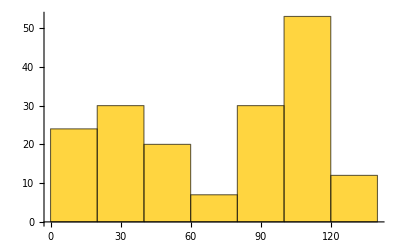

```mathematica
Map[#[[3]]&,WXitvlP]//Histogram
```

```mathematica
toLine[kv_]:=Line[{{kv[[1]],kv[[3]]},{kv[[2]],kv[[3]]}}]
```

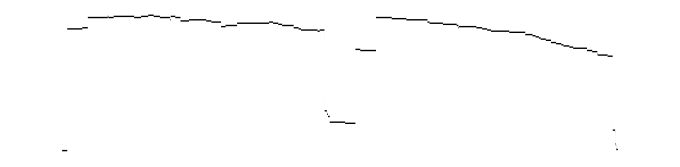

```mathematica
Graphics[Map[toLine,WXitvlP]]
```

### 垂直ブロック抽出(2)

```mathematica
impt4=Import[dir<>file2,"TEXT"];
```

```mathematica
refine4=docrefine[impt4];
```

ページサイズ：

```mathematica
pgSize=Map[#[[1]]&,refine4]
```

{{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89},{0.,0.,595.28,841.89}}

テキストブロック（ページごと）：

```mathematica
pgText=Map[Cases[#,{{_,_,_,_},{__}},{2}]&,refine4];
```

```mathematica
(pgTxCoord=Map[#[[1]]&,pgText,{2}])//Length
```

14

```mathematica
(Yspans=Map[{#[[2]],#[[4]]}&,pgTxCoord,{2}])//Length
```

14

```mathematica
(Yitvl=MapApply[Interval,Yspans])//Length
```

14

```mathematica
WYitvl=Apply[Interval,Cases[Yitvl,List[_,_],Infinity]]
```

Interval[{87.2262,96.8123},{98.2201,772.174}]

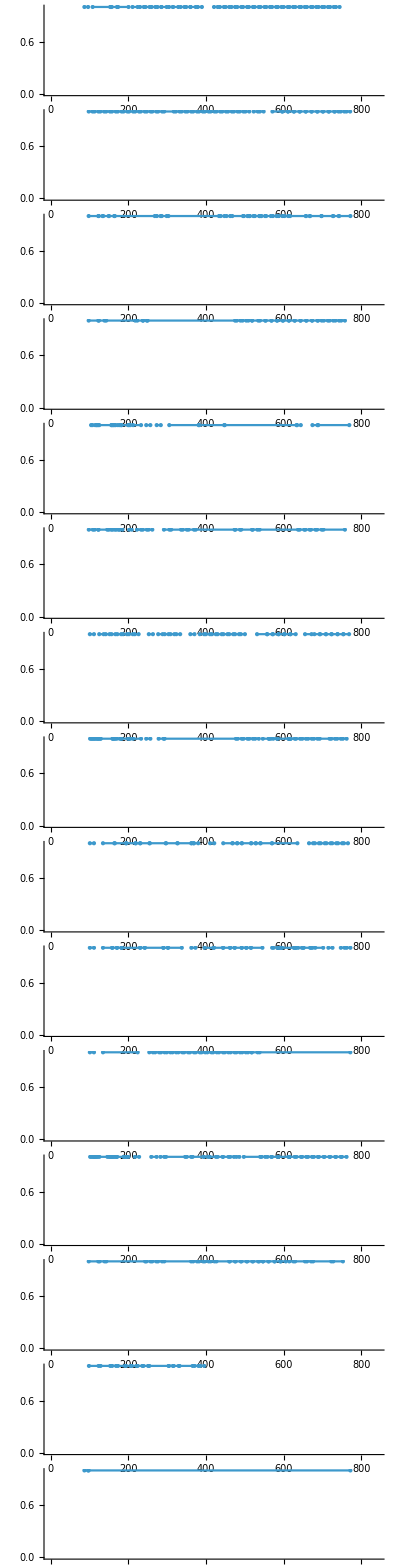

```mathematica
Map[NumberLinePlot[#,PlotRange->{0,841.89},ImageSize->800]&,Append[Yitvl,WYitvl]]//TableForm
```